```mathematica
SetDirectory[NotebookDirectory[]]
If[!DirectoryQ["plots"],CreateDirectory["plots"]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
M=32;
M2=3;
κ=1;
η=0.1;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]
```

/Users/zack/Documents/oscillators/faraday

/Users/zack/Documents/oscillators/faraday/plots

## Equations

```mathematica
Clear[κ]
Clear[η]
Clear[L]
xhat={1,0};
zhat={0,1};
A[i_,j_]:={0,a*m}
a=γ*L0*ω^2;
g=L0;
m=1;
x[i_,j_,t_]:={L[i]*Sin[θ[i][t]],-L[i]*Cos[θ[i][t]]}
Δ[i_,j_,t_]:=(-m*g*zhat+κ*((x[i+1,j,t]+δ*xhat+(L[i+1]-L[i])*zhat-(x[i,j,t]))+(x[i-1,j,t]-δ*xhat+(L[i-1]-L[i])*zhat-(x[i,j,t])))+A[i,j]*Cos[t]+T*x[i,j,t]);
eqn=FullSimplify[{Cos[θ[i][t]],Sin[θ[i][t]]}.(m*ω^2*D[x[i,j,t],{t,2}]-Δ[i,j,t]+η*ω*D[x[i,j,t],t])/(L0*m)]
κ=1;
η=0.1;
```

1/L0((L0-L0 γ ω^2 Cos[t]-κ L[1+i]) Sin[θ[i][t]]-κ L[-1+i] (Sin[θ[-1+i][t]-θ[i][t]]+Sin[θ[i][t]])+κ L[1+i] Sin[θ[i][t]-θ[1+i][t]]+L[i] (2 κ Sin[θ[i][t]]+η ω θ[i]'[t]+ω^2 θ[i]''[t]))

## Linear dispersion and candidate random cases

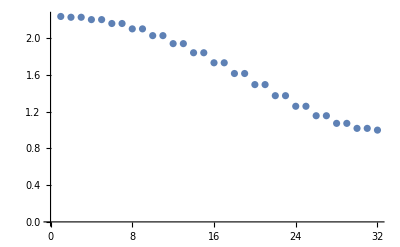

0.390181

data/frequencies1.dat

```mathematica
L0=1;
g=1;
lengths=ConstantArray[0,M];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
ListPlot[(4*#-η^2)^(1/2)/2&/@evals]
frequencies1=(4*#-η^2)^(1/2)/2&/@evals;

Max[Differences[Sort[evals][[1;;M/2+5]]]]
Export["data/frequencies1.dat",frequencies1]
```

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies2=(4*#-η^2)^(1/2)/2&/@evals;
Export["data/frequencies2.dat",frequencies2]
```

data/frequencies2.dat

{0.185063,Null}

{0.851452,0.797721,10}

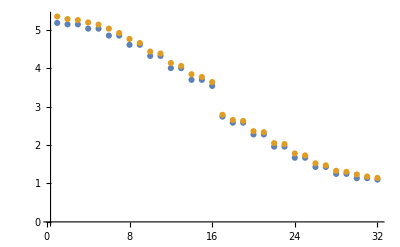

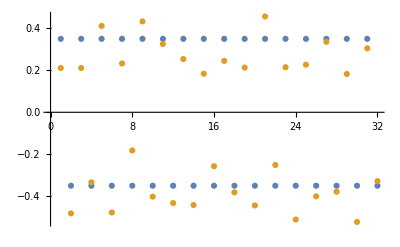

data/frequencies3.dat

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
trials={};
AbsoluteTiming[Monitor[Do[
maxlengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[n]<>".dat"]];
If[Min[maxlengths]>-0.9*L0,
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+5]]]],maxevals,maxevecs,maxlengths}];],{n,1,10}];,n]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,maxevals,maxevecs,maxlengths}=trials[[9]];
{max,Max[Differences[Sort[evals][[1;;M/2+5]]]],Length[trials]}
ListPlot[{evals,maxevals},PlotRange->All]
ListPlot[{lengths,maxlengths}]
frequencies3=(4*#-η^2)^(1/2)/2&/@maxevals;
Export["data/frequencies3.dat",frequencies3]
```

{98.7035,Null}

{0.86899,0.797721,10000}

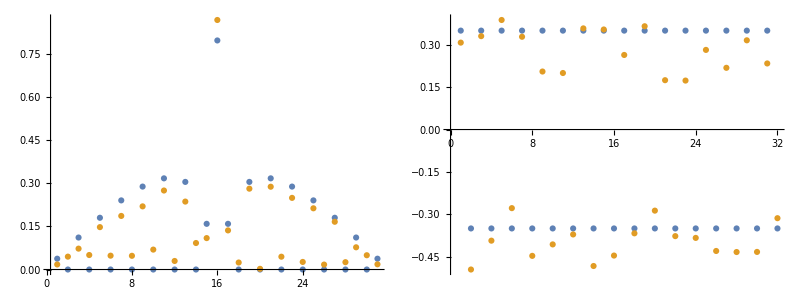

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
time0=AbsoluteTime[];
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies=(4*#-η^2)^(1/2)/2&/@evals;
trials={};
n0=1*10^6;
nmax=10^4;
ϵ=0.5;
Δ2=Δ/(1+ϵ^2/3)^(1/2);
AbsoluteTiming[Monitor[Do[time=AbsoluteTime[];
SeedRandom[n0+n];
maxlengths=Riffle[ConstantArray[Δ2,M/2],ConstantArray[-Δ2,M/2]]+RandomReal[{-ϵ*Δ2,ϵ*Δ2},M];
maxlengths=Δ/Mean[maxlengths^2]^(1/2)*maxlengths; (* normalize for strict constraint of heterogeneity magnitude *)
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+1]]]],maxevals,maxevecs,maxlengths}];,{n,1,nmax}];,N[PaddedForm[{n/nmax, time-time0,(time-time0)*(1-n/nmax)/(n/nmax)} ,{6,6}]]]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,Max[Differences[Sort[evals][[1;;M/2+1]]]],Length[trials]}
Grid[{{ListPlot[{Abs[Differences[evals]],Abs[Differences[maxevals]]},PlotRange->All],ListPlot[{lengths,maxlengths}]}}]
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
```

```mathematica
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
Do[Export["data/randomlengths/randomlengths"<>ToString[i]<>".dat", list[[i]]],{i,1,Length[list]}]
```

## Inhomogeneous Floquet

```mathematica
mat1[s_,ω_,lengths_]:=ArrayFlatten[Table[((1+lengths[[i]])*(-ω^2*(s+n)^2+I*ω*η*(s+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]*KroneckerDelta[n,m]-κ*(1+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,M},{j,1,M}]];
mat2[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,M},{j,1,M}]];
```

{11.4139,Null}

data/boundary1.dat

{11.0122,Null}

data/boundary2.dat

{11.1407,Null}

data/boundary3.dat

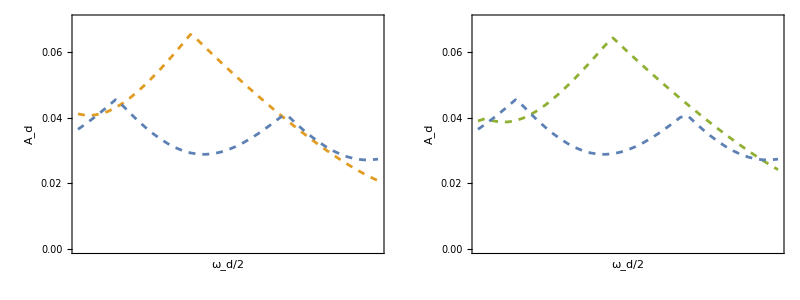

```mathematica
Δ=0.35;
lengths=ConstantArray[0,M];
AbsoluteTiming[boundary1=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["data/boundary1.dat",boundary1]
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[boundary2=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["data/boundary2.dat",boundary2]
lengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
AbsoluteTiming[boundary3=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["data/boundary3.dat",boundary3]
Grid[{{Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary2,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],PlotRange->{{ωmin,ωmax},{0,0.07}},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]],Axes->False,Frame->True],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]],Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary3,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],PlotRange->{{ωmin,ωmax},{0,0.07}},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],Dashed,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]],Axes->False,Frame->True],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]]}}]
```

```mathematica
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary2,u_/;u[[1]]==ω],Cases[boundary2,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary3,u_/;u[[1]]==ω],Cases[boundary3,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
```

0.287035

0.30352

## Direct simulations

```mathematica
rate2[γ_,ω_,lengths_]:=
Module[{tmax,dt,t1,pbcs,eqns,ics,sol,norms,maxes,θ,t,Δ,fourier,q0,β,freq},
Δ[i_]:=lengths[[Mod[i-1,M]+1]];
tmax=2*Pi*100;
t1=2*Pi*50;
dt=2*Pi*0.05;
pbcs={θ[0]->θ[M],θ[M+1]->θ[1]};
eqns=Table[0==(1+ 2*κ (1+Δ[i])-γ ω^2 Cos[t]) θ[i][t]-κ θ[-1+i][t] (1+Δ[-1+i])-κ θ[1+i][t] (1+Δ[1+i])+(1+Δ[i]) (η ω θ[i]'[t]+ω^2 θ[i]''[t])/.pbcs,{i,1,M}];
ics=Join[Table[θ[i][0]==Sum[10^-3*(Sin[q*i]+Cos[q*i]),{q,0,Pi,2*Pi/M}],{i,1,M}],Table[θ[i]'[0]==0,{i,1,M}]];
sol=NDSolve[{eqns,ics},Table[θ[i],{i,1,M}],{t,0,tmax}];
norms=Table[Sum[Abs[θ[i][t]]^2,{i,1,M}]/M/.sol[[1]],{t,t1,tmax,dt}];
If[MemberQ[Differences[Sign[Differences[norms]]],-2],
maxes=1+First/@Position[Differences[Sign[Differences[norms]]],-2];
fourier=Abs[Fourier[Table[(θ[i]/.sol[[1]])[maxes[[-1]]*dt],{i,1,M}]]][[1;;M/2+1]];
q0=(First@FirstPosition[fourier,Max[fourier]]-1)*2*Pi/M;
β=D[Fit[Transpose[{dt*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x];
freq=N[Max[{#,1-#}]&@((First@FirstPosition[#,Max[#]]-1)/((tmax-t1)/(2*Pi))&@Mean[Table[Abs[Fourier[Table[(θ[i][t]/.sol[[1]])/Exp[β/2*t],{t,t1,tmax,dt}]]][[1;;Round[(tmax-t1)/dt/2]]],{i,1,M}]])];
{q0,γ,ω,freq,If[norms[[maxes[[-1]]]] > norms[[maxes[[1]]]],β,-1],Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Transpose[{dt*maxes/(2*Pi),Log[Abs[norms[[maxes]]]]/Log[10]}],Table[θ[i]/.sol[[1]],{i,1,M}]},{0,γ,ω,1/(dt/(Pi)*Mean[Differences[maxes]]),-1,Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Table[θ[i]/.sol[[1]],{i,1,M}]}]]
```

{0.773831,Null}

{π/2,0.04,3.5,0.5,0.010282}

{0.722375,Null}

{(3 π)/8,0.04,3.5,0.56,-1}

{0.747366,Null}

{π/16,0.04,3.5,0.68,-1}

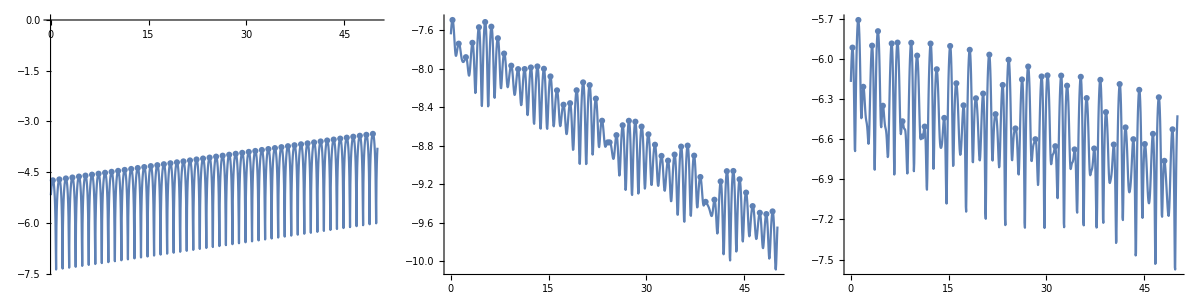

```mathematica
lengths=ConstantArray[0,M];
AbsoluteTiming[{q0,γ0,ω0,f0,β,norms,maxes,sol}=rate2[0.04,3.5,lengths];]
{q0,γ0,ω0,f0,β}
p1=Show[ListPlot[norms,Joined->True,PlotRange->All],ListPlot[maxes,Joined->False,PlotRange->All]];
lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
AbsoluteTiming[{q0,γ0,ω0,f0,β,norms,maxes,sol}=rate2[0.04,3.5,lengths];]
{q0,γ0,ω0,f0,β}
p2=Show[ListPlot[norms,Joined->True,PlotRange->All],ListPlot[maxes,Joined->False,PlotRange->All]];
lengths=Flatten[Import["data/randomlengths/randomlengths"<>ToString[2]<>".dat"]];
AbsoluteTiming[{q0,γ0,ω0,f0,β,norms,maxes,sol}=rate2[0.04,3.5,lengths];]
{q0,γ0,ω0,f0,β}
p3=Show[ListPlot[norms,Joined->True,PlotRange->All],ListPlot[maxes,Joined->False,PlotRange->All]];
Grid[{{p1,p2,p3}}]
```

```mathematica
Npoints=25;
lengths=ConstantArray[0,M];
AbsoluteTiming[Monitor[tongues1=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["data/tongues1.dat",N[tongues1]]
Δ=0.35;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[Monitor[tongues2=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["data/tongues2.dat",N[tongues2]]
lengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
AbsoluteTiming[Monitor[tongues3=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["data/tongues3.dat",N[tongues3]]
```

{191.912,Null}

data/tongues1.dat

{207.02,Null}

data/tongues2.dat

{195.755,Null}

data/tongues3.dat

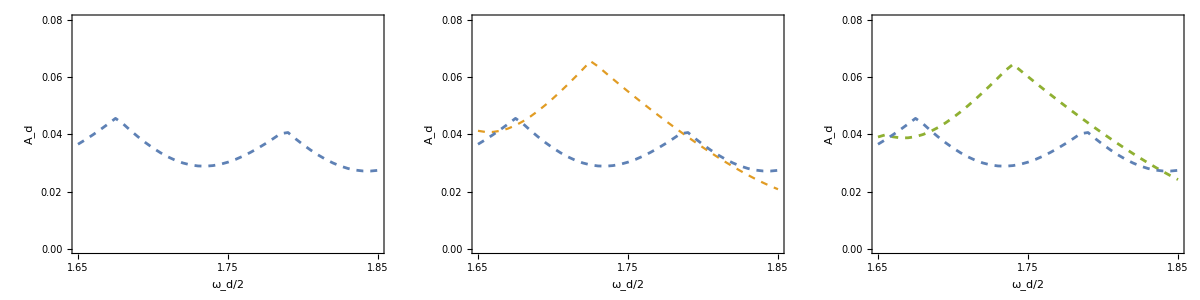

```mathematica
tongues1=Import["data/tongues1.dat"];
tongues2=Import["data/tongues2.dat"];
tongues3=Import["data/tongues3.dat"];
boundary1=Import["data/boundary1.dat"];
boundary2=Import["data/boundary2.dat"];
boundary3=Import["data/boundary3.dat"];
p1=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues1}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
p2=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues2}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary2,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
p3=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues3}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary3,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],Dashed,AbsoluteThickness[2]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
Grid[{{p1,p2,p3}}]
```

```mathematica
Max[boundary1[[All,2]]]
Min[boundary1[[All,2]]]
```

0.0455393

0.027167

```mathematica
Monitor[vals0=Table[Import["data/critical2/"<>ToString[i]<>"_"<>ToString[j]<>"_0out.dat"][[2]],{i,0,30},{j,0,30}],{i,j}];
Monitor[vals1=Table[Import["data/critical2/"<>ToString[i]<>"_"<>ToString[j]<>"_1out.dat"][[2]],{i,0,30},{j,0,30}],{i,j}];
```

```mathematica
vals1
```

{{32,0.5,3.4,0.025,0.,0.,0.2966,0.837758},{32,0.5,3.4,0.0252,0.,0.,0.3401,0.},{32,0.5,3.4,0.0254,0.,0.,0.0461,0.418879},{32,0.5,3.4,0.0256,0.,0.,0.,0.},{32,0.5,3.4,0.0258,0.,0.,0.3441,0.418879},{32,0.5,3.4,0.026,0.,0.,0.,0.},{32,0.5,3.4,0.0262,0.,0.,0.33,0.},{32,0.5,3.4,0.0264,0.,0.,0.,0.},{32,0.5,3.4,0.0266,0.,0.,0.,0.},{32,0.5,3.4,0.0268,0.,0.,0.,0.},{32,0.5,3.4,0.027,0.,0.,0.25,2.93215},{32,0.5,3.4,0.0272,0.,0.,0.2632,0.837758},{32,0.5,3.4,0.0274,0.,0.,0.3661,0.418879},{32,0.5,3.4,0.0276,0.,0.,0.3145,0.418879},{32,0.5,3.4,0.0278,0.,0.,0.,0.},{32,0.5,3.4,0.028,0.,0.,0.3051,0.418879},{32,0.5,3.4,0.0282,0.,0.,0.3822,1.25664},{32,0.5,3.4,0.0284,0.,0.,0.2516,0.},{32,0.5,3.4,0.0286,0.,0.,-0.7208,0.418879},{32,0.5,3.4,0.0288,0.,0.,0.4335,0.},{32,0.5,3.4,0.029,0.,0.,0.2991,0.418879},{32,0.5,3.4,0.0292,0.,0.,0.,0.},{32,0.5,3.4,0.0294,0.,0.,0.,0.},{32,0.5,3.4,0.0296,0.,0.,0.,0.},{32,0.5,3.4,0.0298,0.,0.,0.3319,0.418879},{32,0.5,3.4,0.03,0.,0.,0.4267,0.},{32,0.5,3.4,0.0302,0.,0.,-0.696,0.837758},{32,0.5,3.4,0.0304,0.,0.,-0.5117,0.},{32,0.5,3.4,0.0306,0.,0.,-0.6088,0.418879},{32,0.5,3.4,0.0308,0.,0.,0.25,1.67552},{32,0.5,3.4,0.031,0.,0.,0.2851,0.418879},{32,0.5,3.4,0.0312,0.,0.,0.2952,0.},{32,0.5,3.4,0.0314,0.,0.,0.1187,0.},{32,0.5,3.4,0.0316,0.,0.,0.,0.},{32,0.5,3.4,0.0318,0.,0.,0.359712,0.837758},{32,0.5,3.4,0.032,0.,0.,0.3027,0.837758},{32,0.5,3.4,0.0322,0.,0.,0.4977,0.},{32,0.5,3.4,0.0324,0.,0.,-0.1016,0.},{32,0.5,3.4,0.0326,0.,0.,0.0293,0.418879},{32,0.5,3.4,0.0328,0.,0.,0.1656,0.},{32,0.5,3.4,0.033,0.,0.,-0.6055,0.418879},{32,0.5,3.4,0.0332,0.,0.,0.2725,0.418879},{32,0.5,3.4,0.0334,0.,0.,0.2402,0.418879},{32,0.5,3.4,0.0336,0.,0.,0.2829,0.},{32,0.5,3.4,0.0338,0.,0.,0.2758,0.},{32,0.5,3.4,0.034,0.,0.,0.3181,0.418879},{32,0.5,3.4,0.0342,0.,0.,0.,3.35103},{32,0.5,3.4,0.0344,0.,0.,-0.7134,0.},{32,0.5,3.4,0.0346,0.,0.,-0.4595,0.418879},{32,0.5,3.4,0.0348,0.,0.,-0.4032,0.},{32,0.5,3.4,0.035,0.,0.,0.,0.},{32,0.5,3.4,0.0352,0.,0.,0.,0.},{32,0.5,3.4,0.0354,0.,0.,0.4,3.35103},{32,0.5,3.4,0.0356,0.,0.,0.2822,0.},{32,0.5,3.4,0.0358,0.,0.,0.,0.},{32,0.5,3.4,0.036,0.,0.,-0.6873,0.418879},{32,0.5,3.4,0.0362,0.,0.,0.3132,0.},{32,0.5,3.4,0.0364,0.,0.,-0.6796,0.837758},{32,0.5,3.4,0.0366,0.,0.,0.2921,0.837758},{32,0.5,3.4,0.0368,0.,0.,0.3714,0.}}

## Plots

```mathematica
boundary1=Import["data/boundary1.dat"];
boundary2=Import["data/boundary2.dat"];
boundary3=Import["data/boundary3.dat"];
frequencies1=Flatten[Import["data/frequencies1.dat"]];
frequencies2=Flatten[Import["data/frequencies2.dat"]];
frequencies3=Flatten[Import["data/frequencies3.dat"]];
```

```mathematica
(NIntegrate[Interpolation[Table[First@MinimalBy[Cases[boundary2,u_/;u[[1]]==ω],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
(NIntegrate[Interpolation[Table[First@MinimalBy[Cases[boundary3,u_/;u[[1]]==ω],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
```

0.287035

0.30352

```mathematica
Clear[ω];
p0=Show[Block[{Δ=0},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/2,PlotRange->{1/2,5/2},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{π/4,DisplayForm[RowBox[{"π","/",8}]]},{π/2,DisplayForm[RowBox[{"π","/",4}]]},{(3 π)/4,DisplayForm[RowBox[{3"π","/",8}]]},{π,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,Pi,Pi/4}]}}]],Block[{Δ=0.35},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]]],

ListPlot[Table[{Pi/(M/2)*(i-1),Reverse[frequencies1][[i]]},{i,1,M/2+1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],
ListPlot[Table[{Pi/(M/2)*(i+1),Reverse[frequencies1][[i+1]]},{i,1,M/2,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],
ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies1][[i]]},{i,M/2,M,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies1][[i+1]]},{i,M/2,M-1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],

ListPlot[Table[{Pi/(M/2)*(i-1),Reverse[frequencies2][[i]]},{i,1,M/2+1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],
ListPlot[Table[{Pi/(M/2)*(i+1),Reverse[frequencies2][[i+1]]},{i,1,M/2,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],
ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies2][[i]]},{i,M/2,M,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies2][[i+1]]},{i,M/2,M-1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],

ListPlot[Join[Table[{Pi/(M/2)*(i-1),Reverse[frequencies3][[i]]},{i,1,M/2-1,2}],{{Pi,Reverse[frequencies3][[M/2]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[{{0,Reverse[frequencies3][[1]]}},Table[{Pi/(M/2)*(i+1),Reverse[frequencies3][[i+1]]},{i,1,M/2,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[{{Pi,Reverse[frequencies3][[1+M/2]]}},Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i]]},{i,M/2+2,M,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i+1]]},{i,M/2,M-1,2}],{{0,Reverse[frequencies3][[M]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],

ListPlot[Join[Table[{Pi/(M/2)*(i-1),Reverse[frequencies3][[i]]},{i,1,M/2-1,2}],{{Pi,Reverse[frequencies3][[M/2]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],
ListPlot[Join[{{0,Reverse[frequencies3][[1]]}},Table[{Pi/(M/2)*(i+1),Reverse[frequencies3][[i+1]]},{i,1,M/2,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],
ListPlot[Join[{{Pi,Reverse[frequencies3][[1+M/2]]}},Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i]]},{i,M/2+2,M,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],ListPlot[Join[Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i+1]]},{i,M/2,M-1,2}],{{0,Reverse[frequencies3][[M]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],ImageSize->350,ImagePadding->{{65,15},{65,10}},PlotRange->{{0,Pi+0.1},{1,2.5}}];

p5=Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary2,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Axes->False,Frame->True,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[3]],PlotRange->All,ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[3]]]];
p6=Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary3,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Axes->False,Frame->True,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[3]],PlotRange->All,ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[3]]]];
p3=Grid[{{p0,p5,p6}}]
```

-Graphics-

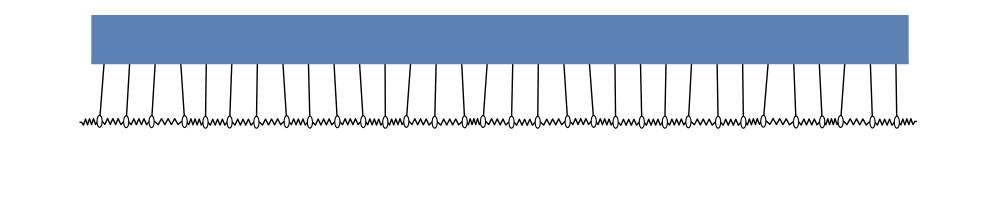
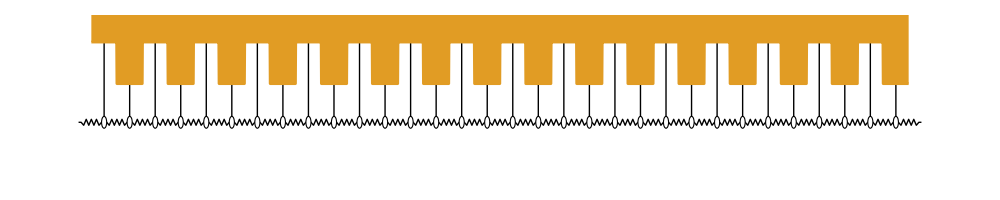
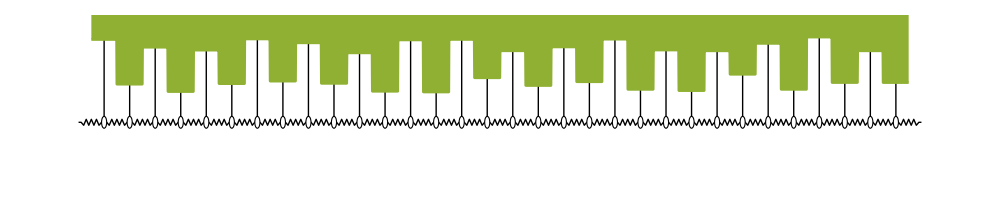
-Graphics-
-Graphics-
-Graphics-
-Graphics-

Export::nodir: Directory /Users/zack/Documents/oscillators/faraday/plots/ does not exist.

Export::noopen: Cannot open plots/fig2.pdf.

$Failed

```mathematica
lengths=ConstantArray[0,M];
thetas=RandomReal[{-Pi/16,Pi/16},M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
p0=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];
Δ=0.35;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
thetas=ConstantArray[0,M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
f[x_]:=lengths[[Round[x]]]
p1=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];

lengths=0.35/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
thetas=ConstantArray[0,M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
f[x_]:=lengths[[Round[x]]]
p2=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];
p=Grid[{{p0},{p1},{p2},{p3}}]
Export["plots/fig2.pdf",p]
```